## Neural networks - Part I

## Introduction to ANNs

Artificial neural networks (ANNs) are models inspired on the functioning of the brain.

### Elements of ANN

ANNs consists of artificial neurons connected by edges

In a brain, neurons are wired to other neurons forming a network. 

Biological neurons receive input signals coming from other neurons, process the information, and send an output:

Artificial neurons mimic this procedure by applying mathematical functions to the I inputs to provide O outputs:

### Neurons layout - Network topology or architecture

Suppose that data consists of M features (x_1,x_2,...,x_M) and the goal of an ANN is to transform it into O outputs  (y_1,y_2,...,y_O). 

For instance, the outputs can be classes or numerical values. Therefore, ANNs can be used for both classification and prediction.

The most common layout of ANNs consists of a layer structure:

Input layer: A neuron for each feature in the input data.

Hidden layers: These layers take the outputs from the input layer, operate with them and outputs the results to the output layer.

Output layer: Transforms the output of the hidden layers to give the output we are interested in.

#### Number of neurons and layers

Large neural networks may consist of the order of 10^7 neurons. This is still far from the human brain which contains of the order of 10^11 neurons. It was predicted that the number of neurons in ANNs will get to the size of the human brain in 2056 (see the freely available book http://www.deeplearningbook.org/).

The depth of an ANN is the number of layers. Current ANNs can have tens of layers.

Deep neural network (DNN): It is an ANN with multiple hidden layers.

Deep learning refers to training DNNs.

### How can ANNs be used?

Building networks from scratch

Build the network architecture. Decide what layers you need.

Use data to train the network. This defines what each neuron will do to the input data or inputs from other neurons.

Apply the trained network to other data with the same format as the data used to train.

In Mathematica: Use Predict and Classify superfunctions to automatically train networks for prediction and classification.

Use pre-built networks.

For instance, the Wolfram Neural Net Repository is a public resource that hosts an expanding collection of trained and untrained neural network models suitable for immediate evaluation, training, visualization, transfer learning and more.

Do net surgery on pre-built networks.

### Strengths and weaknesses of ANNs

#### Strengths

Can model more complex situations than most other methods in machine learning.

Can be used for both classification and prediction problems.

#### Weaknesses

Computationally intensive.

Slow to train, mainly if the network topology is reasonably complex. GPU can be used to accelerate the process.

Can easily lead to overfitting.

The model behind trained networks is often difficult (or impossible) to interpret by humans.

### Additional Bibliography for ANNs

Neural networks are covered in all books recommended on machine learning. There are many other books and articles on the topic. 

Freely available book online: Ian Goodfellow and Yoshua Bengio and Aaron Courville http://www.deeplearningbook.org/

Charu C. Aggarwal “Neural Networks and Deep Learning”, Springer (2018)

Yann LeCun, Yoshua Bengio & Geoffrey Hinton “Deep Learning”, Nature 521, 436 (2015).

A. Zhang, Z.C. Lipton, M. Li and A. J. Smola, “Dive into deep learning”, (2020) https://d2l.ai/

The Mathematica tutorial on Neural Networks is also very instructive: Neural Networks in the Wolfram Language

## Understanding ANNs through simple examples

Linear and logistic regression can be seen as simple ANNs.

### ANN for linear regression

Let us consider data with just one feature, x. Linear regression can predict the value of a dependent variable y by assuming that it is a linear combination of x. 

This can be viewed as an ANN with a single layer. This is called a linear layer:

#### Defining the layer - LinearLayer

Mathematica has many layers implemented. The linear layer is the most basic layer:

```mathematica
linearNet=LinearLayer["Output"-> "Real","Input"->"Real"]
```

LinearLayer[<>]

The syntax is  LinearLayer[O,”Input”→I], where I is the number of input variables and O is the number of output variables (both equal to 1 in our simple example)

#### Get information on the layer - Information

Applying the Information function on ANNs we can obtain a lot of information:

```mathematica
Information[linearNet,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

For instance, the number of layers in this case is simply

```mathematica
Information[linearNet,"LayersCount"]
```

1

```mathematica
Information[linearNet,"LayersList"]
```

{LinearLayer[<>]}

#### Initializing the network - NetInitialize

Notice that in the summary box above, there is an “uninitialized” caption indicating that the net contains learnable parameters that have not yet been provided. In this case, these are the parameters w_0 and w_1

Using NetInitialize, we can give random values to the parameters:

```mathematica
initializedLinear=NetInitialize[linearNet]
```

LinearLayer[<>]

The values of the initialized parameters can be extracted using the NetExtract function.

The parameter w_0 is called bias within the LinearLayer function:

```mathematica
NetExtract[initializedLinear,"Biases"]
```

NumericArray[…]

```mathematica
w0=NetExtract[initializedLinear,"Biases"]//Normal
```

{0.}

The parameter w_1 is called weight within the LinearLayer function:

```mathematica
w1=NetExtract[initializedLinear,"Weights"]//Normal
```

{{-0.428227}}

```mathematica
w1=Flatten[w1][[1]]
```

-0.428227

#### Applying the network to data (before training)

We can readily apply networks to input data:

```mathematica
initializedLinear[3.17]
```

-1.35748

```mathematica
w0+w1*3.17
```

{-1.35748}

#### Training the network - NetTrain

The function NetTrain allows us to train the network using data. In this simple example, training consists in finding the parameters w_0 and w_1.

Here, I use the same data we used to illustrate the functioning of linear regression:

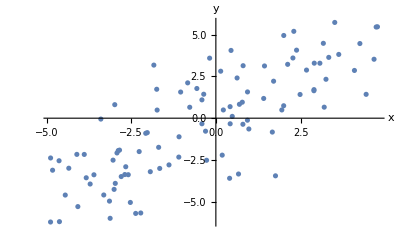

```mathematica
SeedRandom[1];
trainingData=Table[x->x+RandomVariate[NormalDistribution[0, 2]], {x, RandomReal[{-5, 5}, 100]}];
ListPlot[List@@@trainingData,AxesLabel->{"x","y"}]
```

```mathematica
Take[trainingData,5]
```

{3.17389→4.48574,-3.8858→-2.17134,2.89526→1.64482,-3.12197→-5.99774,-2.58639→-3.38662}

```mathematica
Take[List@@@trainingData,5]
```

{{3.17389,4.48574},{-3.8858,-2.17134},{2.89526,1.64482},{-3.12197,-5.99774},{-2.58639,-3.38662}}

```mathematica
trainedNet=NetTrain[linearNet,trainingData]
```

LinearLayer[<>]

Once the network has been trained, it can be applied to input data to get an output:

```mathematica
trainedNet[3.17389]
```

3.07534

Parameters of the model:

```mathematica
NetExtract[trainedNet,"Biases"]
```

NumericArray[…]

```mathematica
NetExtract[trainedNet,#]&/@{"Biases","Weights"} //Normal
```

{{0.103163},{{0.936445}}}

If we had a dataset in which data points are characterised by two features, one should use “Input”→”Vector” to define the linear layer

```mathematica
trainingData2={{1,1}->12.9,{2,2}->8.2,{3,3}->6.9,{4,4}->3.1};
```

```mathematica
trainedNet2=NetTrain[LinearLayer["Output"->"Real","Input"->"Vector"],trainingData2]
```

LinearLayer[<>]

Visualizing the fit:

```mathematica
plotFitData[predictor_,data_,xmin_,xmax_]:=Module[{p=predictor,data0=data,xmin0=xmin,xmax0=xmax,x},
Show[Plot[p[x],
{x,xmin0,xmax0},
PlotStyle->{Blue},PlotLegends->{"Prediction"}],ListPlot[data0,PlotStyle->Red,PlotLegends->{"Data"}]]]
```

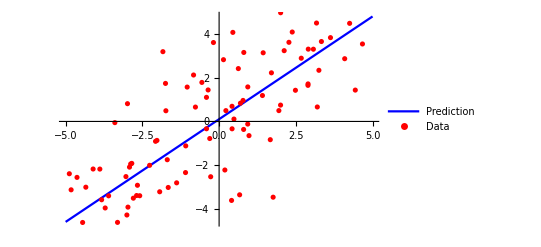

```mathematica
plotFitData[trainedNet,List@@@trainingData,-5,5]
```

#### Summarising training information

Specifying All in NetTrain gives a NetTrainResultsObject[…] that summarizes information about the training session.

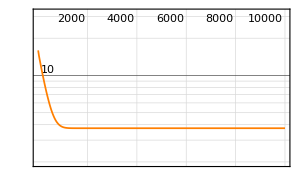
NetTrain Results
summary | ,,  batches:20000  rounds:10000  time:28s  examples/s:45770
data | ,,  training examples:100  processed examples:1280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.74
 | rounds
loss | -Graphics- | 
 |

```mathematica
results=NetTrain[linearNet,trainingData,All,MaxTrainingRounds->1000]
```

### ANN for logistic regression

#### Setting the ANN

Logistic regression can be viewed as a simple two-layer ANN: A linear neuron followed by a sigmoid neuron:

In fact, this model resembles what a biological neuron is believed to do: Gather information (input), transform it (integrate) and give a signal out (fire) or not, depending on the strength of the integrated signal.

In Mathematica, a sigmoid neuron can be implemented as an ElementwiseLayer with LogisticSigmoid shape.

Here, I use the NetGraph command to concatenate the two layers ({1,2} means that the input of the second element,  ElementwiseLayer[LogisticSigmoid], is the output of the first, LinearLayer[]):

```mathematica
logistic=NetGraph[{LinearLayer[],ElementwiseLayer[LogisticSigmoid]},{1->2}]
```

NetGraph[<>]

Indeed, one can check that the network consists of two layers:

```mathematica
Information[logistic,"LayersCount"]
```

2

Note that the input and output format of the linear layer have not been specified. In this way, the format remains general until we initialize the network or train it.

In this case, one could also concatenate the two layers using NetChain:

```mathematica
logistic2=NetChain[{LinearLayer[],ElementwiseLayer[LogisticSigmoid]}]
```

NetChain[<>]

The logistic net will be used below but logistic2 would give equivalent results.

#### Training the ANN

```mathematica
tDLog={1.2->0,2.1->0,3.4->0,5.1->1,7.3-> 1,9.7-> 1};
trainedLogistic=NetTrain[logistic,tDLog]
```

NetGraph[<>]

#### Visualising the fitted function

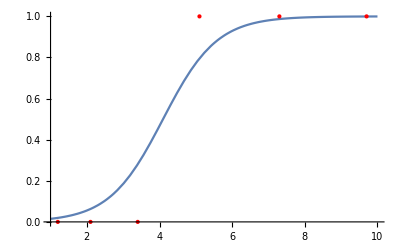

```mathematica
Show[Plot[trainedLogistic[x],{x,1,10}],ListPlot[List@@@tDLog,PlotStyle->{Red,PointSize[Medium]}]]
```

```mathematica
Information[trainedLogistic,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[trainedLogistic,"SummaryGraphic"]
```

-Graphics-

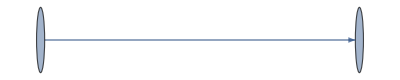

```mathematica
Information[trainedLogistic,"LayersGraph"]
```

## ANN Layers in Mathematica

So far, we have just used two types of layers: LinearLayer and ElementwiseLayer[LogisticSigmoid] 

However, Mathematica offers many layers to build neural networks

```mathematica
?*Layer
```

### Basic layers

The basic layers are LinearLayer and ElementwiseLayer[]

The functioning of LinearLayer has been illustrated above.

ElementwiseLayer[f] can be used to apply any function f to every element of the input of the layer.

The function f is referred to as the activation function in the literature; commonly used activation functions are LogisticSigmoid, Tanh and Ramp (Rectified Linear Unit, ReLU):

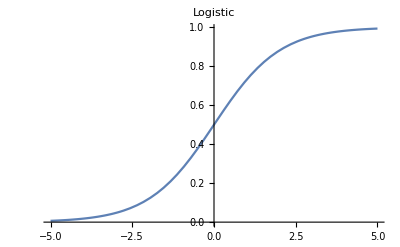
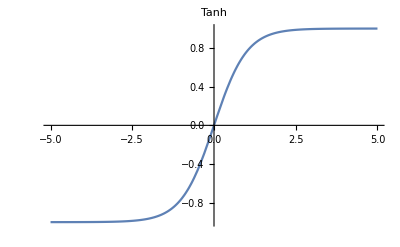
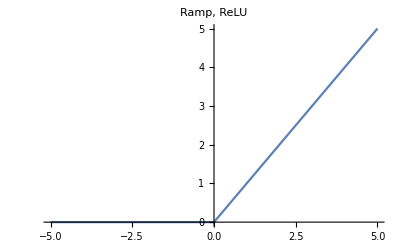

```mathematica
{Plot[LogisticSigmoid[x],{x,-5,5},PlotLabel->"Logistic"],
Plot[Tanh[x],{x,-5,5},PlotLabel->"Tanh"],
Plot[Ramp[x],{x,-5,5},PlotLabel->"Ramp, ReLU"]}
```

```mathematica
layer=ElementwiseLayer[Tanh]
```

ElementwiseLayer[<>]

```mathematica
data=RandomReal[{-5,5},10]
layer[data]
```

{-2.75074,4.62366,-2.78941,-0.41268,-0.579986,-1.67176,-1.06027,2.5566,2.13444,-2.86009}

{-0.991872,0.999807,-0.992474,-0.390746,-0.522655,-0.931784,-0.785768,0.988038,0.972391,-0.993463}

## Automated training of neural networks for prediction and classification

### Automated prediction with ANNs

Let us consider the same type of data as used above for linear regression:

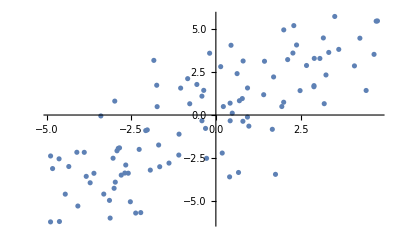

```mathematica
SeedRandom[1];
data=Table[x->x+RandomVariate[NormalDistribution[0, 2]], {x, RandomReal[{-5, 5}, 100]}];
ListPlot[List@@@data]
```

The Predict function can be used to train a predictor based on a neural network:

```mathematica
pNN=Predict[data,Method->"NeuralNetwork"]
```

PredictorFunction[…]

```mathematica
Information[pNN,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each unit computes its value as a 
function of the unit values in the previous layer. Information is processed layer by layer from the feature layer to the 
output unit which gives the predicted value. It is also called a feed-forward neural network or a multi-layer perceptron.

#### Training times

You might have noticed that training the neural network predictor took significantly longer than training a predictor using the linear regression method. 

In order to compare, let us train a predictor using the linear regression method:

```mathematica
pLR=Predict[data,Method->"LinearRegression"]
```

PredictorFunction[…]

The neural network model takes almost 20 times longer than the linear regression model to be trained:

```mathematica
Information[pNN,"TrainingTime"]
```

35.0087 s

```mathematica
Information[pLR,"TrainingTime"]
```

1.24709 s

#### Visualizing the fitted model

```mathematica
plotSDRegion[predictor_,data_,xmin_,xmax_]:=Module[{p=predictor,data0=data,xmin0=xmin,xmax0=xmax,x},
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,xmin0,xmax0},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[data0,PlotStyle->Red,PlotLegends->{"Data"}]]]
```

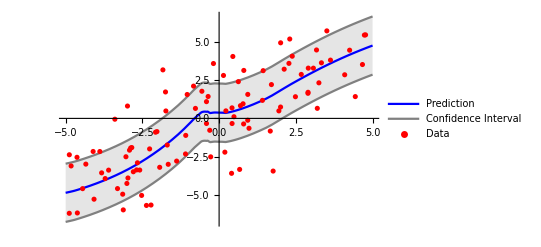

```mathematica
plotSDRegion[pNN,List@@@data,-5,5]
```

The fitted model is not simply linear regression!

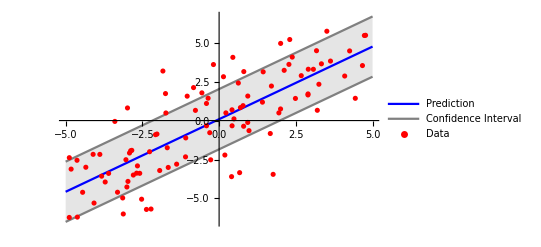

```mathematica
plotSDRegion[pLR,List@@@data,-5,5]
```

#### Exploring the network used by Predict

Technical information on the trained model can be obtained with the following command:

```mathematica
pNN[[1]]
```

<|ExampleNumber→100,Input→<|Preprocessor→ToMLDataset,Processor→  ToVector→ImputeMissing→Standardize|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→Standardize→FromVector→FirstValues,ProbabilityPostprocessor→Identity,InverseProcessorFunction→(-0.244492+3.13172 #1&),ProcessorFunction→(0.0780698+0.319314 #1&),Name→value,Quantiles→{-1.9082,1.90979}|>,Prior→Automatic,Utility→(DiracDelta[#2-#1]&),Threshold→0,PerformanceGoal→Automatic,BatchProcessing→Automatic,Model→<|Method→NeuralNetwork,Network→NetGraph[<>],Training→<|Optimizer→{ADAM,L2Regularization→None},TrainingProgressFunction→{Null&,Interval→1},TotalTrainingTime→1.22753,MeanInputsPerSecond→31282.3|>,InputType→NumericalVector,Processor→  Standardize→FirstValues,FeatureNumber→1,DistributionData→{NormalDistribution,Automatic},PostProcessor→Identity,Options→<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→2,Options→<||>|>,NumberOfParameters→<|Value→2600,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→300,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→None,Options→<||>|>|>|>,TrainingInformation→<|PanelCell→44657,TrainingFunction→Predict,EMIterations→Missing[KeyAbsent,EMIterations],ProcessorEntropyShift→1.14158,PreprocessingTime→0.338096,LossName→StandardDeviation,BestModelInformation→,Configurations→,MaxTrainingSize→100,PreprocessorEvaluationTime→5.9×10^-6,PreprocessorMemory→39312,InputDimension→1,OutputDimension→1,BaselineLogProbability→-1.41894,VariableBudget→True,CheckpointingInfo→<|Checkpointing→False|>,UserStop→False,NaturalStop→True,AbortStop→False,LastReportingTime→3.8150303354959622×10^9,RoundPartitioning→|>,AnomalyDetector→None,Log→<|Example→ | Type | Weight | Values
f1 | Numerical | 1 | { -0.4116 }
1 examples | no weights | grouped examples | no density weights |  |  | Dataset[Association[(_String -> _Association)..]],TrainingTime→35.0087,MaxTrainingMemory→1645552,DataMemory→9664,FunctionMemory→267696,LanguageVersion→{12.1,1},Date→Sun 22 Nov 2020 10:38:57GMT,ProcessorCount→4,ProcessorType→x86-64,OperatingSystem→Windows,SystemWordLength→64,Evaluations→{}|>|>

This is an association. The model used is the entry [“Model”][“Network”] in the association:

```mathematica
netLinear=pNN[[1]]["Model"]["Network"]
```

NetGraph[<>]

```mathematica
Information[pNN,"Properties"]
```

{BatchEvaluationSpeed,BatchEvaluationTime,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,MaxTrainingRounds,MeanCrossEntropy,Method,MethodDescription,MethodOption,NetworkDepth,PerformanceGoal,Properties,StandardDeviation,TrainingTime,UtilityFunction}

The network consists of two layers. This can be seen from the output above or using

```mathematica
Information[pNN,"NetworkDepth"]
```

2

One can extract particular layers using NetExtract.

The first layer is

```mathematica
layer1=NetExtract[netLinear,1]
```

NetChain[<>]

In fact, this is a container: a layer containing more elementary layers.

```mathematica
Head[layer1]
```

NetChain

In fact a NetChain object can be viewed as a list:

```mathematica
layer1//Normal
```

{LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>]}

We can see individual elements as usual with lists:

```mathematica
layer1[[-1]]  (*last layer in layer1*)
```

LinearLayer[<>]

```mathematica
NetExtract[layer1[[-1]],"Biases"]
```

NumericArray[…]

```mathematica
NetExtract[layer1[[-1]],"Weights"]//Normal
```

{{0.0660444,-0.036722,-0.0120828,0.0912465,-0.081405,-0.035633,0.188074,0.172879,0.14827,-0.0282826,-0.135006,0.0771517,-0.278722,0.417588,-0.122024,0.0444668,-0.1512,0.11558,0.0277695,-0.056986,-0.149402,-0.120733,-0.171356,0.0862946,0.0751706,-0.251808,0.121827,0.0850447,0.0471273,0.0357241,-0.116988,-0.12306,-0.0425134,-0.0694645,0.184035,0.00713996,0.0667523,0.0444001,-0.0380112,0.22818,-0.0751885,-0.0789502,0.0258265,0.0628286,0.0626205,0.0584241,-0.0464987,-0.113603,0.00225039,0.040533}}

#### Controlling the depth of the network

It is possible to control the depth of the network used by Predict

```mathematica
pDepth=Predict[data,Method->{"NeuralNetwork","NetworkDepth"->10}]
```

PredictorFunction[…]

```mathematica
Information[pDepth,"TrainingTime"]
```

25.611 s

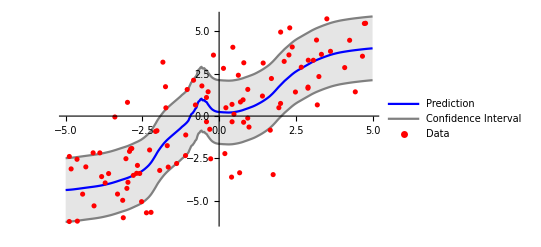

```mathematica
plotSDRegion[pDepth,List@@@data,-5,5]
```

```mathematica
pDepth[[1]]["Model"]["Network"]
```

NetGraph[<>]

#### Overfitting

Using a very deep network might look fashionable given the appeal of deep learning and might work well sometimes.

However, by using many layers, we might end up overfitting unless we have a big enough dataset.
 
Overfitting is the failure of a model to generalize to data outside of the training set.

In the previous example, using a deeper network seems to adapt better to the particular fluctuations of the dataset. However, if we increase the size of the dataset, predictions might not be reliable to the model with many layers.

### Automated classification with Neural networks

The Classify function can be used to automatically train a neural network to predict classes.

Feel free to go through this subsection yourself. It is similar to the previous subsection on prediction but now dealing with classification.

```mathematica
c=Classify[{1,2,3,4}->{"A","A","B","B"},Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
Information[c,"TrainingTime"]
```

5.63404 s

#### Properties of the trained classifier

```mathematica
Information[c,"Properties"]
```

{Accuracy,BatchEvaluationSpeed,BatchEvaluationTime,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,MaxTrainingRounds,MeanCrossEntropy,Method,MethodDescription,MethodOption,NetworkDepth,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

How many layers?

```mathematica
Information[c,"NetworkDepth"]
```

2

```mathematica
Information[c,"LearningCurve"]
```

The panel “Learning curves for all algorithms” gives the loss function. The final value can be seen looking at the mean cross entropy which is the loss function used to train the ANN.

```mathematica
Information[c,"MeanCrossEntropy"]
```

0.520.34

#### Exploring the trained network

The specific network trained by the classifier can be retrieved from the Classify function as follows:

```mathematica
c[[1]]
```

<|ExampleNumber→4,ClassNumber→2,Input→<|Preprocessor→ToMLDataset,Processor→  ToVector→ImputeMissing→Standardize|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→IntegerEncodeNominalVector→FromVector→FirstValues,ProbabilityPostprocessor→Identity,Name→class,Marginal→<|A→0.5,B→0.5|>|>,Prior→Automatic,Utility→SparseArray[…],Threshold→0,TieBreaker→RandomChoice,PerformanceGoal→Automatic,BatchProcessing→Automatic,Model→<|Method→NeuralNetwork,Network→NetChain[<>],Training→<|Optimizer→{ADAM,L2Regularization→None},TrainingProgressFunction→{Null&,Interval→1},TotalTrainingTime→1.79374,MeanInputsPerSecond→2229.98|>,InputType→NumericalVector,Processor→  Standardize→FirstValues,FeatureNumber→1,PostProcessor→Identity,Options→<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→2,Options→<||>|>,NumberOfParameters→<|Value→2650,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→1000,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→None,Options→<||>|>|>|>,TrainingInformation→<|PanelCell→70417,TrainingFunction→Classify,EMIterations→Missing[KeyAbsent,EMIterations],ProcessorEntropyShift→0,PreprocessingTime→0.271288,LossName→MeanCrossEntropy,BestModelInformation→,Configurations→,MaxTrainingSize→4,PreprocessorEvaluationTime→5.×10^-6,PreprocessorMemory→39312,InputDimension→1,OutputDimension→1,BaselineLogProbability→-0.693147,VariableBudget→True,CheckpointingInfo→<|Checkpointing→False|>,UserStop→False,NaturalStop→True,AbortStop→False,LastReportingTime→3.8150333222881934×10^9,RoundPartitioning→|>,AnomalyDetector→None,Log→<|Example→ | Type | Weight | Values
f1 | Numerical | 1 | { 4 }
1 examples | no weights | grouped examples | no density weights |  |  | Dataset[Association[(_String -> _Association)..]],TrainingTime→5.63404,MaxTrainingMemory→927912,DataMemory→392,FunctionMemory→203640,LanguageVersion→{12.1,1},Date→Sun 22 Nov 2020 11:28:44GMT,ProcessorCount→4,ProcessorType→x86-64,OperatingSystem→Windows,SystemWordLength→64,Evaluations→{}|>|>

The command c[[1]] is an association and we can extract the network as follows:

```mathematica
netc=c[[1]]["Model"]["Network"]
```

NetChain[<>]

```mathematica
Information[netc,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[netc,"LayersCount"]
```

5

```mathematica
Information[netc,"SummaryGraphic"]
```

-Graphics-

```mathematica
layers=Information[netc,"Layers"]
```

<|{1}→LinearLayer[<>],{2}→ElementwiseLayer[<>],{3}→LinearLayer[<>],{4}→ElementwiseLayer[<>],{5}→LinearLayer[<>]|>

```mathematica
layers[{1}]
```

LinearLayer[<>]

```mathematica
NetExtract[layers[{1}],"Weights"]//Normal
```

{{-1.3736},{0.13925},{1.3854},{-0.261118},{-0.983375},{-1.14488},{-1.3638},{0.95787},{-1.85826},{-1.05583},{-0.285141},{-0.178695},{-0.115867},{-1.19956},{0.970789},{-0.752213},{1.07133},{1.08549},{-0.0671327},{-0.39502},{1.10437},{0.499619},{-0.722603},{-0.805032},{0.675757},{-0.103672},{-0.0761446},{-0.572465},{0.72298},{0.948046},{-0.230956},{-1.07842},{-0.568382},{-0.110615},{-0.833385},{2.58392},{-0.220545},{0.555702},{-1.00653},{0.595368},{-1.52411},{1.30386},{-0.50108},{0.508461},{1.99874},{1.53877},{0.337936},{-0.412201},{-0.133664},{0.0452654}}

```mathematica
prob=c[Table[x,{x,0,5,0.1}],"Probabilities"]
```

{<|A→0.999999,B→1.30242×10^-6|>,<|A→0.999999,B→1.319×10^-6|>,<|A→0.999999,B→1.33753×10^-6|>,<|A→0.999999,B→1.35971×10^-6|>,<|A→0.999999,B→1.38465×10^-6|>,<|A→0.999999,B→1.41154×10^-6|>,<|A→0.999999,B→1.44013×10^-6|>,<|A→0.999999,B→1.47216×10^-6|>,<|A→0.999998,B→1.50846×10^-6|>,<|A→0.999998,B→1.55257×10^-6|>,<|A→0.999998,B→1.60475×10^-6|>,<|A→0.999998,B→1.66415×10^-6|>,<|A→0.999998,B→1.73322×10^-6|>,<|A→0.999998,B→1.81923×10^-6|>,<|A→0.999998,B→1.92187×10^-6|>,<|A→0.999998,B→2.04723×10^-6|>,<|A→0.999998,B→2.20773×10^-6|>,<|A→0.999998,B→2.42378×10^-6|>,<|A→0.999997,B→2.70658×10^-6|>,<|A→0.999997,B→3.09221×10^-6|>,<|A→0.999996,B→3.66115×10^-6|>,<|A→0.999995,B→4.59453×10^-6|>,<|A→0.999994,B→6.33622×10^-6|>,<|A→0.999989,B→0.0000106839|>,<|A→0.999966,B→0.0000343163|>,<|A→0.779804,B→0.220196|>,<|A→0.0000310407,B→0.999969|>,<|A→3.73225×10^-6,B→0.999996|>,<|A→1.37498×10^-6,B→0.999999|>,<|A→7.43567×10^-7,B→0.999999|>,<|A→4.86604×10^-7,B→1.|>,<|A→3.56797×10^-7,B→1.|>,<|A→2.82083×10^-7,B→1.|>,<|A→2.34479×10^-7,B→1.|>,<|A→2.0131×10^-7,B→1.|>,<|A→1.7815×10^-7,B→1.|>,<|A→1.60904×10^-7,B→1.|>,<|A→1.47309×10^-7,B→1.|>,<|A→1.36778×10^-7,B→1.|>,<|A→1.28963×10^-7,B→1.|>,<|A→1.22553×10^-7,B→1.|>,<|A→1.16974×10^-7,B→1.|>,<|A→1.12242×10^-7,B→1.|>,<|A→1.08038×10^-7,B→1.|>,<|A→1.04668×10^-7,B→1.|>,<|A→1.01777×10^-7,B→1.|>,<|A→9.9027×10^-8,B→1.|>,<|A→9.665×10^-8,B→1.|>,<|A→9.46982×10^-8,B→1.|>,<|A→9.31767×10^-8,B→1.|>,<|A→9.19393×10^-8,B→1.|>}

```mathematica
Values[prob]
```

{{0.999999,1.30242×10^-6},{0.999999,1.319×10^-6},{0.999999,1.33753×10^-6},{0.999999,1.35971×10^-6},{0.999999,1.38465×10^-6},{0.999999,1.41154×10^-6},{0.999999,1.44013×10^-6},{0.999999,1.47216×10^-6},{0.999998,1.50846×10^-6},{0.999998,1.55257×10^-6},{0.999998,1.60475×10^-6},{0.999998,1.66415×10^-6},{0.999998,1.73322×10^-6},{0.999998,1.81923×10^-6},{0.999998,1.92187×10^-6},{0.999998,2.04723×10^-6},{0.999998,2.20773×10^-6},{0.999998,2.42378×10^-6},{0.999997,2.70658×10^-6},{0.999997,3.09221×10^-6},{0.999996,3.66115×10^-6},{0.999995,4.59453×10^-6},{0.999994,6.33622×10^-6},{0.999989,0.0000106839},{0.999966,0.0000343163},{0.779804,0.220196},{0.0000310407,0.999969},{3.73225×10^-6,0.999996},{1.37498×10^-6,0.999999},{7.43567×10^-7,0.999999},{4.86604×10^-7,1.},{3.56797×10^-7,1.},{2.82083×10^-7,1.},{2.34479×10^-7,1.},{2.0131×10^-7,1.},{1.7815×10^-7,1.},{1.60904×10^-7,1.},{1.47309×10^-7,1.},{1.36778×10^-7,1.},{1.28963×10^-7,1.},{1.22553×10^-7,1.},{1.16974×10^-7,1.},{1.12242×10^-7,1.},{1.08038×10^-7,1.},{1.04668×10^-7,1.},{1.01777×10^-7,1.},{9.9027×10^-8,1.},{9.665×10^-8,1.},{9.46982×10^-8,1.},{9.31767×10^-8,1.},{9.19393×10^-8,1.}}

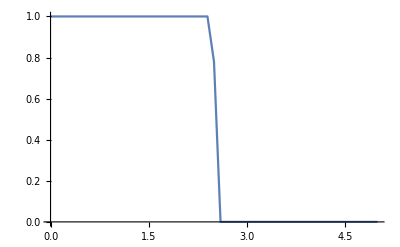

```mathematica
ListPlot[Transpose[{Table[x,{x,0,5,0.1}],Values[prob][[All,1]]}],Joined->True]
```

## Universal Approximation Theorem

The Universal Approximation Theorem that, under quite general conditions, a feedforward ANN with a single layer can approximate any continuous function with any degree of accuracy if the layer contains enough neurons.

### Using neural networks to approximate functions

In numerical analysis of data, it is often useful to fit a function to the data. 

A typical way to do this is to fit polynomials (a+b x+c x^2+...). However, this might not be very efficient if the data has a complicated structure.

Following from the universal approximation theorem, neural networks can be trained to fit any function to an arbitrary degree of accuracy. We just need to use enough nodes in our network.

Consider, for instance data that obeys the following function:

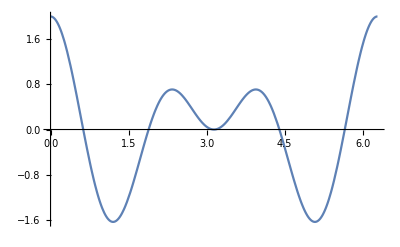

```mathematica
Plot[{Cos[2 x]+Cos[3 x]},{x,0,2 Pi}]
```

Our data might be random (in some way). Here, I consider 5000 data points:

```mathematica
data=(#->Cos[2 #]+Cos[3 #])&@RandomReal[{0,2 Pi},5000];
```

```mathematica
Take[Values[data],10]
```

{0.337041,-0.0788513,-0.302779,0.706188,0.130354,-0.921409,1.99276,1.19256,0.699475,1.99786}

```mathematica
Take[Keys[data],10]
```

{2.0132,4.4246,1.78734,3.97068,3.37697,4.68661,0.0333902,5.91553,2.3899,6.26504}

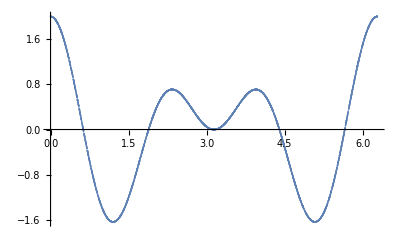

```mathematica
dataplot=Transpose[{Keys[data],Values[data]}];
ListPlot[dataplot]
```

Let us train a net with four outputs from a linear layer modified by a logistic activation function:

```mathematica
fNet4:=NetChain[{LinearLayer[4],ElementwiseLayer[LogisticSigmoid],LinearLayer[1]},"Input"->"Real","Output"->NetDecoder["Scalar"]]
```

```mathematica
trainfNet4=NetTrain[fNet4,data]
```

NetChain[<>]

And one with 10 outputs:

```mathematica
fNet10:=NetChain[{LinearLayer[10],ElementwiseLayer[LogisticSigmoid],LinearLayer[1]},"Input"->"Real","Output"->NetDecoder["Scalar"]]
```

```mathematica
trainfNet10=NetTrain[fNet10,data]
```

NetChain[<>]

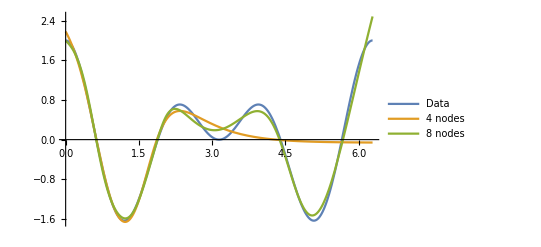

```mathematica
Plot[{Cos[2 x]+Cos[3 x],trainfNet4[x],trainfNet10[x]},{x,0,2 Pi},PlotLegends->{"Data","4 nodes", "10 nodes"}]
```